# Entanglements code behavior

## Simple Entanglements

Simple entanglements generate a single chain of interdependent elements. This system is visualized using two columns. The left column show the random input used at each step of the entanglement. On the right column, we observe the output of the entanglement rules. The rule is the bitwise XOR of the output at the previous step and the current random input. Therefore, at step i, the array is formed with {rn[[i]], BitXor[rn[[i]], array[[i-1]][[2]]]}. Because the entanglement defines a single chain, there is only one initial condition showed on the first row at position [[1]][[2]].

Showing 10 steps

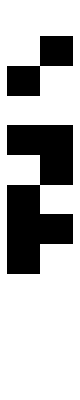

```mathematica
With[
{rn=RandomInteger[1,10]},
MapThread[ReplacePart[#1,1-> #2]&,{FoldList[BitXor[#1,#2]&,PadLeft[{1},2],rn],Prepend[rn,0]}]]//ArrayPlot
```

Showing 100 steps

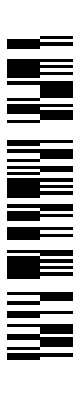

```mathematica
With[
{rn=RandomInteger[1,100]},
MapThread[ReplacePart[#1,1-> #2]&,{FoldList[BitXor[#1,#2]&,PadLeft[{1},2],rn],Prepend[rn,0]}]]//ArrayPlot
```

## Complex Entanglements

Complex entanglements define multiple chains that are intertwined together.

### Helical Entanglement Codes

Helical Entanglement Codes (p-HEC) are complex entanglements that use two horizontal chains (H_1 and H_2), and two kinds of p helical chains (right-handed strands RH_1...RH_p and left-handed strands LH_1...LH_p). These codes generate a total of 2 + (2 × p) chains (we also used the term “strands”). 
Each individual strand corresponds to a simple entanglement. All strands from the same type will generate one encoded version of the input data. Each individual input data is injected to three strands, all of them of different type. That means that the input data must be distributed to distinct strands. Helical entanglement codes use two horizontal strands. That means that the input data D is divided by two. The number of helical strands is p, that means that the input data D is divided by p. That means that from step D/p+1 the strand does not contain any value to show unless more data is inserted in the system and more steps are shown in the visualization. In our first example, 2-HEC the length of horizontal and helical strands is identical because p = 2.

#### 2-HEC

```mathematica
rand=RandomInteger[1,100]; (* Data injected to the 2-HEC automaton*)
```

```mathematica
entangle[data_]:=FoldList[BitXor,{0},data] (* Rule with initial condition = 1 *)
```

In this example we extract from rand the data used in each strand and compute the entanglement for each strand showing all the steps.

Horizontal Strands

Horizontal chain H1

```mathematica
dataOddNodes=Partition[rand,2][[All,1]](* Data that is stored at odd nodes *)
```

{1,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,1,0,0,1,1,0,0,1}

```mathematica
chainH1 = entangle[dataOddNodes]//Flatten
```

{0,1,0,0,1,1,1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,0,1,0,1,0,0,1,0,0,0,1,1,1,1,0,0,0,1,0,0,0,1}

Horizontal chain H2

```mathematica
dataEvenNodes=Partition[rand,2][[All,2]] (* Data that is stored at even nodes*)
```

{1,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,0,1}

```mathematica
chainH2=entangle[dataEvenNodes]//Flatten
```

{0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1}

Helical Strands

Right-handed chain RH1

```mathematica
dataRH1 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,1,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1}

```mathematica
chainRH1 = entangle[dataRH1]//Flatten
```

{0,1,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1}

Right-handed chain RH2

```mathematica
dataRH2 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,2,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,1,1,0,0,1}

```mathematica
chainRH2=entangle[dataRH2]//Flatten
```

{0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1}

Left-handed chain LH1

```mathematica
dataLH1 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,1,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1}

```mathematica
chainLH1=entangle[dataLH1]//Flatten
```

{0,1,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1}

Left-handed chain LH2

```mathematica
dataLH2 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,2,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

```mathematica
{1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,1,1,0 0,1}
```

```mathematica
chainLH2 = entangle[dataLH2]//Flatten
```

{0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1}

Visualization

This example shows 50 steps in the evolution of the rules. The first row (step 0) shows the initial conditions for the six strands. In the example all strands are initialized with zero. The data injected to the automaton, which contains random data, is shown at the left of the grid (columns 1-2). The rest of the columns (3-9) shown the outputs of the entanglements, i.e. all the encoded elements of the six entanglement strands in the following order: H1, H2, RH1, RH2, LH1, and LH2. Each of these columns are equivalent to the output of a single entanglement. Input data that is injected at step i is used at the same step for some strands, but other strands use inputs after certain delay. In particular, horizontal strands always use input data in the same step in which the data was injected.

```mathematica
Transpose[{Prepend[dataOddNodes,0],Prepend[dataEvenNodes,0],chainH1,chainH2,chainRH1,chainRH2,chainLH1,chainLH2}]//ArrayPlot
```

-Graphics-

Observations: 2-HEC has a particular behavior. Since p = 2 some strands are connecting the same vertices and therefore the sequence we observe in one column is replicated in another column. In particular RH1 is identical to LH1 and RH2 is identical to LH2. This situation will not happen with with p > 2. If we use different initial conditions for the pairs of identical strands, one of the columns will become the negative inverted image of the other.

#### p-HEC (p > 2)

In the previous example of 2-HEC we did each computation step by step. Below, we use a code snippet that computes everything in a more compact way.

```mathematica
ClearAll
input = RandomInteger[1,10]
{inputH1,inputH2}={Partition[input,2] [[All,1]],Partition[input,2] [[All,2]]}
```

ClearAll

{1,1,0,0,1,0,0,0,0,1}

{{1,0,1,0,0},{1,0,0,0,1}}

### Test area

#### 3-HEC

```mathematica
rand3 =RandomInteger[1,100]; (* Data injected to the 2-HEC automaton*)
```

```mathematica
entangle[data_]:=FoldList[BitXor,{0},data] (* Rule with initial condition = 1 *)
```

In this example we extract from rand the data used in each strand and compute the entanglement for each strand showing all the steps.

Horizontal Strands

Horizontal chain H1

```mathematica
dataOddNodes=Partition[rand,2][[All,1]](* Data that is stored at odd nodes *)
```

{1,1,0,1,0,0,1,1,1,0,1,0,1,1,1,0,1,1,0,1,1,0,1,0,1,1,0,1,0,1,1,1,1,0,1,1,0,0,1,0,0,0,1,0,0,1,1,0,0,1}

```mathematica
chainH1 = entangle[dataOddNodes]//Flatten
```

{0,1,0,0,1,1,1,0,1,0,0,1,1,0,1,0,0,1,0,0,1,0,0,1,1,0,1,1,0,0,1,0,1,0,0,1,0,0,0,1,1,1,1,0,0,0,1,0,0,0,1}

Horizontal chain H2

```mathematica
dataEvenNodes=Partition[rand,2][[All,2]] (* Data that is stored at even nodes*)
```

{1,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,1,0,0,0,0,1,0,1,0,1,0,1,1,0,0,0,0,1,1,0,1}

```mathematica
chainH2=entangle[dataEvenNodes]//Flatten
```

{0,1,0,0,0,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,1,0,0,0,1,0,0,0,0,0,1,1,1,1,1,0,0,1,1,0,0,1,0,0,0,0,0,1,0,0,1}

Helical Strands

Right-handed chain RH1

```mathematica
dataRH1 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,1,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1}

```mathematica
chainRH1 = entangle[dataRH1]//Flatten
```

{0,1,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1}

Right-handed chain RH2

```mathematica
dataRH2 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,2,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,1,1,0,0,1}

```mathematica
chainRH2=entangle[dataRH2]//Flatten
```

{0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1}

Left-handed chain LH1

```mathematica
dataLH1 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,1,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,0,0,0,1,1,1,0,1,0,1,0,1,0,1,0,0,0,1,0,1,1,1,0,0,0,0,1,1,0,1,0,1,0,0,0,1,0,0,1,1,0,0,0,1,1,0,1}

```mathematica
chainLH1=entangle[dataLH1]//Flatten
```

{0,1,0,0,0,0,0,1,0,1,1,0,0,1,1,0,0,1,1,1,1,0,0,1,0,1,1,1,1,1,0,1,1,0,0,1,1,1,1,0,0,0,1,0,0,0,0,1,0,0,1}

Left-handed chain LH2

```mathematica
dataLH2 = Part[rand,Most@NestWhileList[If[EvenQ[#],#+1,#+3]&,2,#≤ Length[rand]&]](* Auxiliar data - redundant *)
```

{1,1,0,1,0,0,0,1,1,0,0,0,1,1,0,0,0,1,0,1,1,0,0,0,1,1,0,1,0,1,0,1,0,0,1,1,1,0,1,0,1,0,0,0,0,1,1,0,0,1}

```mathematica
chainLH2 = entangle[dataLH2]//Flatten
```

{0,1,0,0,1,1,1,1,0,1,1,1,1,0,1,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,0,0,1,1,1,0,1,0,0,1,1,0,0,0,0,0,1,0,0,0,1}

Visualization

This example shows 50 steps in the evolution of the rules. The first row (step 0) shows the initial conditions for the six strands. In the example all strands are initialized with zero. The data injected to the automaton, which contains random data, is shown at the left of the grid (columns 1-2). The rest of the columns (3-9) shown the outputs of the entanglements, i.e. all the encoded elements of the six entanglement strands in the following order: H1, H2, RH1, RH2, LH1, and LH2. Each of these columns are equivalent to the output of a single entanglement. Input data that is injected at step i is used at the same step for some strands, but other strands use inputs after certain delay. In particular, horizontal strands always use input data in the same step in which the data was injected.

```mathematica
Transpose[{Prepend[dataOddNodes,0],Prepend[dataEvenNodes,0],chainH1,chainH2,chainRH1,chainRH2,chainLH1,chainLH2}]//ArrayPlot
```

-Graphics-

Observations: 2-HEC has a particular behavior. Since p = 2 some strands are connecting the same vertices and therefore the sequence we observe in one column is replicated in another column. In particular RH1 is identical to LH1 and RH2 is identical to LH2. This situation will not happen with with p > 2. If we use different initial conditions for the pairs of identical strands, one of the columns will become the negative inverted image of the other.